```mathematica
Needs["ExperimentEvaluation`"]
```

## Experiments I

```mathematica
data=readAllFiles[{"20110803/GP4D_1000","GPAT4D_SSM_500"},labels,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"]
```

{GPAT_MAZE_MAP2_NOVER,GPAT_MAZE_MAP2_ORIG,GPAT_MAZE_MAP2_RF4,GPAT_MAZE_MAP2_RF8,GPAT_MAZE_MAP3_NOVER,GPAT_MAZE_MAP3_ORIG,GPAT_MAZE_MAP3_RF4,GPAT_MAZE_MAP3_RF8,GPAT_MAZE_MAP4_NOVER,GPAT_MAZE_MAP4_ORIG,GPAT_MAZE_MAP4_RF4,GPAT_MAZE_MAP4_RF8}

```mathematica
data=readAllFiles[(StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GP_MAZE_MAP*"])~Join~(StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"])~Join~{"GPATGP_MAZE_ALL"},labels];
```

```mathematica
names=Flatten@Transpose@{{"GP_MAZE_MAP2_ORIG","GP_MAZE_MAP2_RF4","GP_MAZE_MAP2_RF8","GP_MAZE_MAP2_NOVER","GP_MAZE_MAP3_ORIG","GP_MAZE_MAP3_RF4","GP_MAZE_MAP3_RF8","GP_MAZE_MAP3_NOVER"},{"GPAT_MAZE_MAP2_ORIG","GPAT_MAZE_MAP2_RF4","GPAT_MAZE_MAP2_RF8","GPAT_MAZE_MAP2_NOVER","GPAT_MAZE_MAP3_ORIG","GPAT_MAZE_MAP3_RF4","GPAT_MAZE_MAP3_RF8","GPAT_MAZE_MAP3_NOVER"}};
```

```mathematica
labels={"GP_MAP2_NOVER","GP_MAP2_ORIG","GP_MAP2_RF4","GP_MAP2_RF8","GP_MAP3_NOVER","GP_MAP3_ORIG","GP_MAP3_RF4","GP_MAP3_RF8","GP_MAP4_NOVER","GP_MAP4_ORIG","GP_MAP4_RF4","GP_MAP4_RF8","GPAT_MAP2_NOVER","GPAT_MAP2_ORIG","GPAT_MAP2_RF4","GPAT_MAP2_RF8","GPAT_MAP3_NOVER","GPAT_MAP3_ORIG","GPAT_MAP3_RF4","GPAT_MAP3_RF8","GPAT_MAP4_NOVER","GPAT_MAP4_ORIG","GPAT_MAP4_RF4","GATP_MAP4_RF8","GPATGP_MAP2_ORIG","GPATGP_MAP2_NOVER","GPATGP_MAP2_RF4","GPATGP_MAP2_RF8","GPATGP_MAP3_ORIG","GPATGP_MAP3_NOVER","GPATGP_MAP3_RF4","GPATGP_MAP3_RF8","GPATGP_MAP24_ORIG","GPATGP_MAP4_NOVER","GPATGP_MAP4_RF4","GPATGP_MAP4_RF8"};
```

```mathematica
data=readAllFiles[names,labels];
```

```mathematica
listAllFiles[{"GP_4D_FC55_1000_old","GPAT_4D_FC55_ALL"}]
```

{{/Users/drchaj1/java/exp/GP_4D_FC55_1000_old/experiments_010.txt,/Users/drchaj1/java/exp/GP_4D_FC55_1000_old/parameters_010.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_001.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_001.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_002.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_002.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_003.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_003.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_004.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_004.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_005.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_005.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_006.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_006.txt}}

```mathematica
names={"GP_MAP2_200_old","GPAT_MAP2_ALL","GP_2D_H_1000_old","GPAT_2D_H_ALL","GP_4D_F_1000_old","GPAT_4D_F_ALL","GP_4D_FC55_1000_old","GPAT_4D_FC55_ALL"};
labels=Flatten[Outer[StringJoin[#2,#1]&,{"MAP2","2D_H","4D_F","4D_FC55"},{"GP_","GPAT_BASIC_","GPAT_RANDOM_","GPAT_CONSTANT1_","GPAT_SIMPLE_","GPAT_SIMPLE_REC_","GPAT_SIMPLE_REC2_","GPAT_SIMPLE_REC3_","GPAT_SIMPLE_ROOTO_","GPAT_SIMPLE_REC4_","GPAT_SIMPLE_SIMPLE2_","GPAT_SIMPLE_REC5_"}]];
data=readAllFiles[names,labels];
```

```mathematica
StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"]
```

{GPAT_MAZE_MAP2_NOVER,GPAT_MAZE_MAP2_ORIG,GPAT_MAZE_MAP2_RF4,GPAT_MAZE_MAP2_RF8,GPAT_MAZE_MAP3_NOVER,GPAT_MAZE_MAP3_ORIG,GPAT_MAZE_MAP3_RF4,GPAT_MAZE_MAP3_RF8,GPAT_MAZE_MAP4_NOVER,GPAT_MAZE_MAP4_ORIG,GPAT_MAZE_MAP4_RF4,GPAT_MAZE_MAP4_RF8}

```mathematica
keepOnlyBest[StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPATGP_MAZE_ALL"],"BSF",60]
```

```mathematica
changingParameters[data]
```

{GPAT.FUNCTION_IMPL,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,SOLVER,SYMBOLIC_REGRESSION_4D.F}

```mathematica
sortedData = data;
```

```mathematica
sortedData=sortDataByParams[data,{"SYMBOLIC_REGRESSION_4D.F"},ReplaceParamValues->{"ZFC55"->"FC55"}];
```

```mathematica
data=readAllFiles[{"GPAT_4D_FC55_ALL","A"}];
```

```mathematica
saveData[data,"B"]
```

```mathematica
printAsTable[sortedData,{"SOLVER","MAZE.MAP","SYMBOLIC_REGRESSION_4D.F","GP.TARGET_FITNESS","GP.TYPE","GPAT.FUNCTION_IMPL","GPAT.MUTATION_HEAVY_PROB","GPAT.MUTATION_HEAVY_POWER","GPAT.SPECIES_SIZE_MEAN"}]
```

ID | PARAM FILE | SOLVER | MAZE.MAP | SYMBOLIC_REGRESSION_4D.F | GP.TARGET_FITNESS | GP.TYPE | GPAT.FUNCTION_IMPL | GPAT.MUTATION_HEAVY_PROB | GPAT.MUTATION_HEAVY_POWER | GPAT.SPECIES_SIZE_MEAN
GP_MAP2 | GP_MAP2_200_old/parameters_001.txt | GP | map2.csv | NONE | 50. | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_MAP2 | GPAT_MAP2_ALL/parameters_001.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_MAP2 | GPAT_MAP2_ALL/parameters_002.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_MAP2 | GPAT_MAP2_ALL/parameters_003.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_MAP2 | GPAT_MAP2_ALL/parameters_004.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_MAP2 | GPAT_MAP2_ALL/parameters_005.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_MAP2 | GPAT_MAP2_ALL/parameters_006.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_MAP2 | GPAT_MAP2_ALL/parameters_007.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_MAP2 | GPAT_MAP2_ALL/parameters_008.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_MAP2 | GPAT_MAP2_ALL/parameters_009.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_MAP2 | GPAT_MAP2_ALL/parameters_010.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_MAP2 | GPAT_MAP2_ALL/parameters_011.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_2D_H | GP_2D_H_1000_old/parameters_008.txt | GP | NONE | NONE | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_2D_H | GPAT_2D_H_ALL/parameters_001.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_2D_H | GPAT_2D_H_ALL/parameters_002.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_2D_H | GPAT_2D_H_ALL/parameters_003.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_2D_H | GPAT_2D_H_ALL/parameters_004.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_2D_H | GPAT_2D_H_ALL/parameters_005.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_2D_H | GPAT_2D_H_ALL/parameters_006.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_2D_H | GPAT_2D_H_ALL/parameters_007.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_2D_H | GPAT_2D_H_ALL/parameters_008.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_2D_H | GPAT_2D_H_ALL/parameters_009.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_2D_H | GPAT_2D_H_ALL/parameters_010.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_2D_H | GPAT_2D_H_ALL/parameters_011.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_4D_F | GP_4D_F_1000_old/parameters_006.txt | GP | NONE | F | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_4D_F | GPAT_4D_F_ALL/parameters_001.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_4D_F | GPAT_4D_F_ALL/parameters_002.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_4D_F | GPAT_4D_F_ALL/parameters_003.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_4D_F | GPAT_4D_F_ALL/parameters_004.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_4D_F | GPAT_4D_F_ALL/parameters_005.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_4D_F | GPAT_4D_F_ALL/parameters_006.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_4D_F | GPAT_4D_F_ALL/parameters_007.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_4D_F | GPAT_4D_F_ALL/parameters_008.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_4D_F | GPAT_4D_F_ALL/parameters_009.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_4D_F | GPAT_4D_F_ALL/parameters_010.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_4D_F | GPAT_4D_F_ALL/parameters_011.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_4D_FC55 | GP_4D_FC55_1000_old/parameters_010.txt | GP | NONE | FC55 | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_4D_FC55 | GPAT_4D_FC55_ALL/parameters_001.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_4D_FC55 | GPAT_4D_FC55_ALL/parameters_002.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_4D_FC55 | GPAT_4D_FC55_ALL/parameters_003.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_4D_FC55 | GPAT_4D_FC55_ALL/parameters_004.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_4D_FC55 | GPAT_4D_FC55_ALL/parameters_005.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_4D_FC55 | GPAT_4D_FC55_ALL/parameters_006.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_4D_FC55 | GPAT_4D_FC55_ALL/parameters_007.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_4D_FC55 | GPAT_4D_FC55_ALL/parameters_008.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_4D_FC55 | GPAT_4D_FC55_ALL/parameters_009.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_4D_FC55 | GPAT_4D_FC55_ALL/parameters_010.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_4D_FC55 | GPAT_4D_FC55_ALL/parameters_011.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.

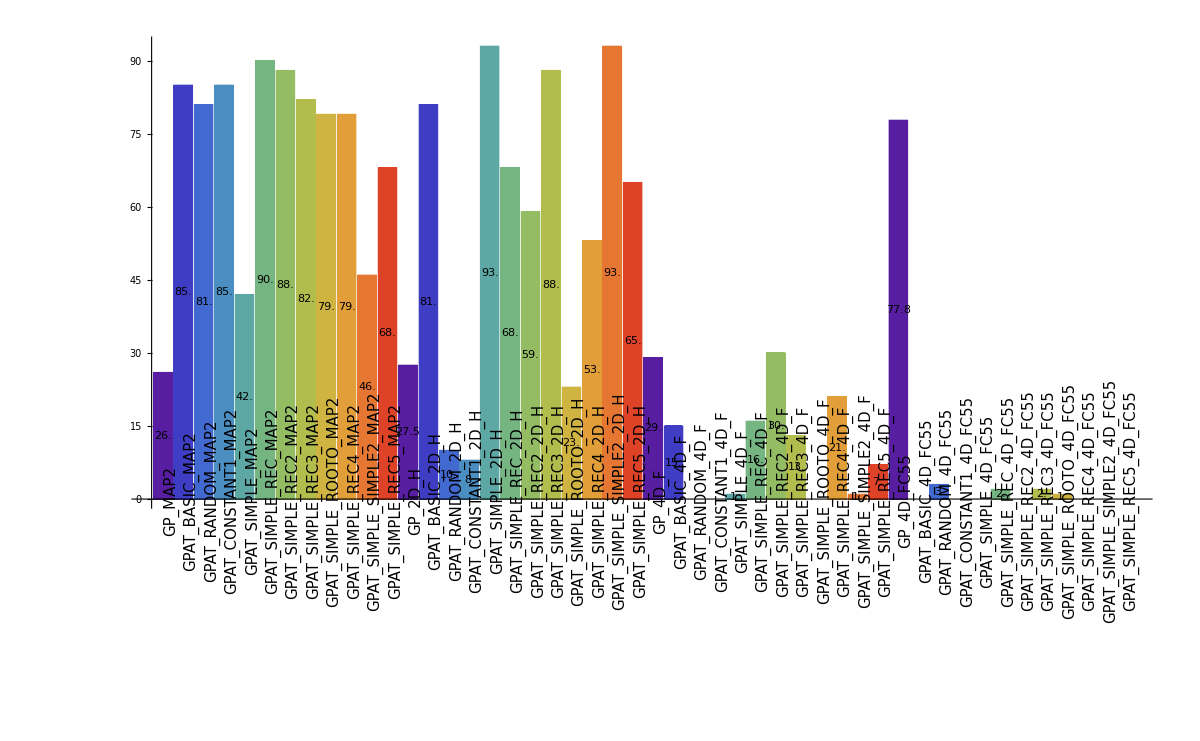

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",12]
```

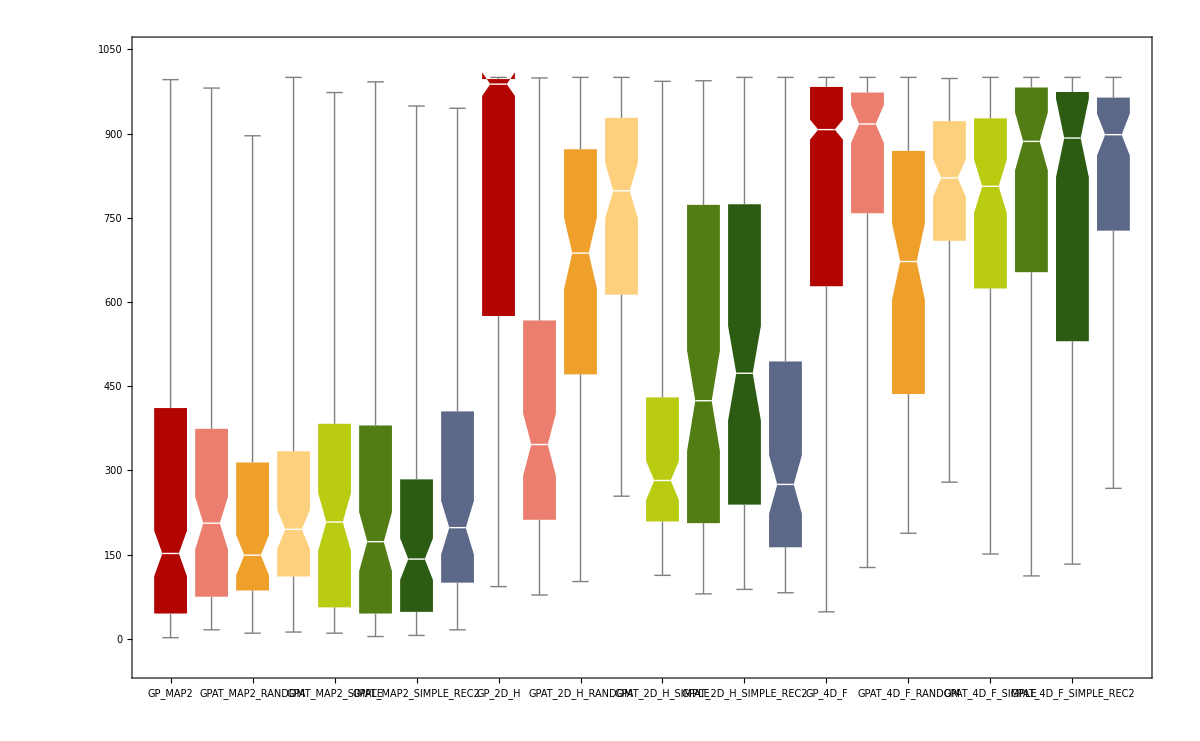

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSFG",8]
```

## Experiments II

```mathematica
names={"GPAT_maze-1_REC7PAR","GPAT_maze-2_REC7PAR"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","PROBLEM","GPAT.DISTANCE","GPAT.DISTANCE_REC5_C1","GPAT.DISTANCE_REC5_C2"},{"ZFC55"->"FC55",RegularExpression["gp.demo.SymbolicRegression.*"]->"","gp.demo.MazeRangeFinders"->"RF4","gp.demo.Maze"->"ORIG","map"->"MAP",".csv"->""}];
changingParameters[data]
```

{GPAT.DISTANCE_REC5_C1,GPAT.DISTANCE_REC5_C2,MAZE.MAP,PROBLEM}

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"CONSTANT","ROOTO","SIMPLE","SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE2","SIMPLE_REC4","SIMPLE_REC5","SIMPLE_REC6"}}];
sortedData = sortDataByParams[sdata,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","SOLVER","GPAT.DISTANCE","PROBLEM"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GP.TARGET_FITNESS","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | SYMBOLIC_REGRESSION.F | MAZE.MAP | GPAT.DISTANCE | GP.TARGET_FITNESS | PROBLEM
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.1 | GPAT_maze-1_REC7PAR/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.5 | GPAT_maze-1_REC7PAR/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.8 | GPAT_maze-1_REC7PAR/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.9 | GPAT_maze-1_REC7PAR/parameters_004.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.95 | GPAT_maze-1_REC7PAR/parameters_005.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.1 | GPAT_maze-1_REC7PAR/parameters_006.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.5 | GPAT_maze-1_REC7PAR/parameters_007.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.8 | GPAT_maze-1_REC7PAR/parameters_008.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.9 | GPAT_maze-1_REC7PAR/parameters_009.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.95 | GPAT_maze-1_REC7PAR/parameters_010.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.1 | GPAT_maze-1_REC7PAR/parameters_011.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.5 | GPAT_maze-1_REC7PAR/parameters_012.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.8 | GPAT_maze-1_REC7PAR/parameters_013.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.9 | GPAT_maze-1_REC7PAR/parameters_014.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.95 | GPAT_maze-1_REC7PAR/parameters_015.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.1 | GPAT_maze-2_REC7PAR/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.5 | GPAT_maze-2_REC7PAR/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.8 | GPAT_maze-2_REC7PAR/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.9 | GPAT_maze-2_REC7PAR/parameters_004.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.95 | GPAT_maze-2_REC7PAR/parameters_005.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.1 | GPAT_maze-2_REC7PAR/parameters_006.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.5 | GPAT_maze-2_REC7PAR/parameters_007.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.8 | GPAT_maze-2_REC7PAR/parameters_008.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.9 | GPAT_maze-2_REC7PAR/parameters_009.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.95 | GPAT_maze-2_REC7PAR/parameters_010.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.1 | GPAT_maze-2_REC7PAR/parameters_011.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.5 | GPAT_maze-2_REC7PAR/parameters_012.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.8 | GPAT_maze-2_REC7PAR/parameters_013.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.9 | GPAT_maze-2_REC7PAR/parameters_014.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.95 | GPAT_maze-2_REC7PAR/parameters_015.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders

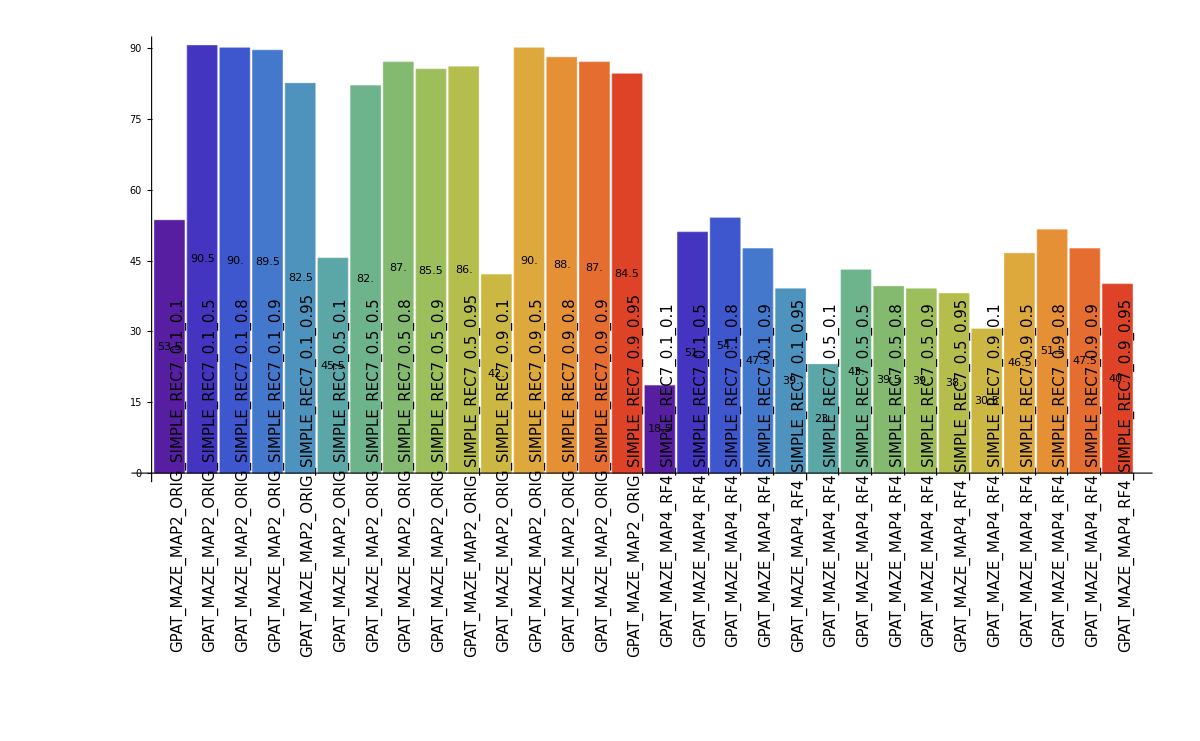

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",15]
```

## Experiments III

```mathematica
(*names={"GP_RANDOMPAR","GP_BASICPAR","GP_RESTO2PAR","GP_TREEPPAR","GP_TREEP2PAR"};*)
(*names={"NEAT_BASIC","NEAT_DELTAS","GP","GP_RANDOM","GP_BASIC","GP_RESTO2","GP_TREEP","GP_TREEP2"};*)
(*names={"GP_GPEFS_GENERAL_GECCO"};*)
names={"NEAT_GECCO","GP","GP_GPEFS_NOGENERAL_GECCO","GP_GPEFS_GENERAL_BEST_GECCO"};
(*names={"NEAT_NOMULT","NEAT_G2000_GECCO","NEAT_P200_GECCO"};*)
(*names={"GP_1D*","GPAT_1D*","GP_2D*","GPAT_2D*"};*)
(*names={"GP_1D*","GPAT_1D*"};*)
(*names={"GP_2D*","GPAT_2D*"};*)
(*names={"GP_3D*","GPAT_3D*"};*)
(*names={"GP_4D*","GPAT_4D*"};*)
(*names={"GP_maze*","GPAT_maze*"};*)
(*names={"GP_1D*","GPAT_1D*","GP_2D*","GPAT_2D*","GP_3D*","GPAT_3D*","GP_4D*","GPAT_4D*","GP_maze*","GPAT_maze*"};*)
(*names={"GP_maze-1_BASIC","GP_maze-2_BASIC"};*)
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","PROBLEM","GPAT.DISTANCE","GP.DISTANCE","GP.DISTANCE_GENERAL_C","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN","NEAT.distanceDelta"},{"ZFC55"->"FC55",RegularExpression["gp.demo.SymbolicRegression.*"]->"","gp.demo.MazeRangeFinders"->"RF4","gp.demo.Maze"->"ORIG","map"->"MAP",".csv"->""}];
changingParameters[data]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.DISTANCE,GP.DISTANCE_GENERAL_C,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.TARGET_FITNESS,GP.TYPE,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SOLVER,SYMBOLIC_REGRESSION.F}

```mathematica
saveData[sortedData,"GP_GPEFS_GENERAL_GECCO2"]
```

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"CONSTANT","ROOTO","SIMPLE","SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE2","SIMPLE_REC4","SIMPLE_REC5","SIMPLE_REC6"}}];*)
sdata=selectData[data,{"ID"->{"1D"}}];
(*sdata=selectData[data,{"GPEFS.SPECIES_REPRODUCTION_RATIO"->{0.4},"GPEFS.SPECIES_SIZE_MEAN"->{5.}}];*)
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GP.DISTANCE_GENERAL_C"}];
(*sortedData = sortDataByParams[data,{"SOLVER"}];*)
extractParameters[sortedData,{
{"SOLVER",{"GP"->"G","NEAT"->"N"}},
{"GP.DISTANCE",{"GENERAL"->"G","BASIC"->"B","ISO"->"I","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}},
{"GPEFS.SPECIES_REPRODUCTION_RATIO",{"0."->"."}}
}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GP.DISTANCE","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | SYMBOLIC_REGRESSION.F | MAZE.MAP | GPAT.DISTANCE | GP.DISTANCE | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | PROBLEM
GP_1D_F_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_001.txt | GP |  | 1D | F |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression
NEAT_1D_F_3. | NEAT_GECCO/parameters_001.txt | NEAT |  | 1D | F |  |  |  |  |  | gp.demo.SymbolicRegression
GP_1D_F | GP/parameters_001.txt | GP |  | 1D | F |  |  |  |  |  | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_001.txt | GP |  | 1D | F |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_F_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_015.txt | GP |  | 1D | F |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_F_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_029.txt | GP |  | 1D | F |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_F_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_043.txt | GP |  | 1D | F |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_057.txt | GP |  | 1D | F |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_002.txt | GP |  | 1D | H |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression
NEAT_1D_H_3. | NEAT_GECCO/parameters_002.txt | NEAT |  | 1D | H |  |  |  |  |  | gp.demo.SymbolicRegression
GP_1D_H | GP/parameters_002.txt | GP |  | 1D | H |  |  |  |  |  | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_002.txt | GP |  | 1D | H |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_016.txt | GP |  | 1D | H |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_030.txt | GP |  | 1D | H |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_044.txt | GP |  | 1D | H |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_058.txt | GP |  | 1D | H |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression
GP_2D_I_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_003.txt | GP |  | 2D | I |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression2D
NEAT_2D_I_3. | NEAT_GECCO/parameters_003.txt | NEAT |  | 2D | I |  |  |  |  |  | gp.demo.SymbolicRegression2D
GP_2D_I | GP/parameters_003.txt | GP |  | 2D | I |  |  |  |  |  | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_003.txt | GP |  | 2D | I |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_017.txt | GP |  | 2D | I |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_031.txt | GP |  | 2D | I |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_045.txt | GP |  | 2D | I |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_059.txt | GP |  | 2D | I |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_004.txt | GP |  | 2D | J |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression2D
NEAT_2D_J_3. | NEAT_GECCO/parameters_004.txt | NEAT |  | 2D | J |  |  |  |  |  | gp.demo.SymbolicRegression2D
GP_2D_J | GP/parameters_004.txt | GP |  | 2D | J |  |  |  |  |  | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_004.txt | GP |  | 2D | J |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_018.txt | GP |  | 2D | J |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_032.txt | GP |  | 2D | J |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_046.txt | GP |  | 2D | J |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_060.txt | GP |  | 2D | J |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_005.txt | GP |  | 2D | K |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression2D
NEAT_2D_K_3. | NEAT_GECCO/parameters_005.txt | NEAT |  | 2D | K |  |  |  |  |  | gp.demo.SymbolicRegression2D
GP_2D_K | GP/parameters_005.txt | GP |  | 2D | K |  |  |  |  |  | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_005.txt | GP |  | 2D | K |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_019.txt | GP |  | 2D | K |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_033.txt | GP |  | 2D | K |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_047.txt | GP |  | 2D | K |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_061.txt | GP |  | 2D | K |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_3D_E_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_006.txt | GP |  | 3D | E |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression3D
NEAT_3D_E_3. | NEAT_GECCO/parameters_006.txt | NEAT |  | 3D | E |  |  |  |  |  | gp.demo.SymbolicRegression3D
GP_3D_E | GP/parameters_006.txt | GP |  | 3D | E |  |  |  |  |  | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_006.txt | GP |  | 3D | E |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_020.txt | GP |  | 3D | E |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_034.txt | GP |  | 3D | E |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_048.txt | GP |  | 3D | E |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_062.txt | GP |  | 3D | E |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_007.txt | GP |  | 3D | H |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression3D
NEAT_3D_H_3. | NEAT_GECCO/parameters_007.txt | NEAT |  | 3D | H |  |  |  |  |  | gp.demo.SymbolicRegression3D
GP_3D_H | GP/parameters_007.txt | GP |  | 3D | H |  |  |  |  |  | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_007.txt | GP |  | 3D | H |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_021.txt | GP |  | 3D | H |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_035.txt | GP |  | 3D | H |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_049.txt | GP |  | 3D | H |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_063.txt | GP |  | 3D | H |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_008.txt | GP |  | 3D | K |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression3D
NEAT_3D_K_3. | NEAT_GECCO/parameters_008.txt | NEAT |  | 3D | K |  |  |  |  |  | gp.demo.SymbolicRegression3D
GP_3D_K | GP/parameters_008.txt | GP |  | 3D | K |  |  |  |  |  | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_008.txt | GP |  | 3D | K |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_022.txt | GP |  | 3D | K |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_036.txt | GP |  | 3D | K |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_050.txt | GP |  | 3D | K |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_064.txt | GP |  | 3D | K |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_4D_C_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_009.txt | GP |  | 4D | C |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression4D
NEAT_4D_C_3. | NEAT_GECCO/parameters_009.txt | NEAT |  | 4D | C |  |  |  |  |  | gp.demo.SymbolicRegression4D
GP_4D_C | GP/parameters_009.txt | GP |  | 4D | C |  |  |  |  |  | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_009.txt | GP |  | 4D | C |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_023.txt | GP |  | 4D | C |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_037.txt | GP |  | 4D | C |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_051.txt | GP |  | 4D | C |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_065.txt | GP |  | 4D | C |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_010.txt | GP |  | 4D | F |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression4D
NEAT_4D_F_3. | NEAT_GECCO/parameters_010.txt | NEAT |  | 4D | F |  |  |  |  |  | gp.demo.SymbolicRegression4D
GP_4D_F | GP/parameters_010.txt | GP |  | 4D | F |  |  |  |  |  | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_010.txt | GP |  | 4D | F |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_024.txt | GP |  | 4D | F |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_038.txt | GP |  | 4D | F |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_052.txt | GP |  | 4D | F |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_066.txt | GP |  | 4D | F |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_011.txt | GP |  | 4D | G |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression4D
NEAT_4D_G_3. | NEAT_GECCO/parameters_011.txt | NEAT |  | 4D | G |  |  |  |  |  | gp.demo.SymbolicRegression4D
GP_4D_G | GP/parameters_011.txt | GP |  | 4D | G |  |  |  |  |  | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_011.txt | GP |  | 4D | G |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_025.txt | GP |  | 4D | G |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_039.txt | GP |  | 4D | G |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_053.txt | GP |  | 4D | G |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_067.txt | GP |  | 4D | G |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_012.txt | GP |  | 4D | ZFC55 |  |  | GENERAL | 0.4 | 5. | gp.demo.SymbolicRegression4D
NEAT_4D_FC55_3. | NEAT_GECCO/parameters_012.txt | NEAT |  | 4D | ZFC55 |  |  |  |  |  | gp.demo.SymbolicRegression4D
GP_4D_FC55 | GP/parameters_012.txt | GP |  | 4D | ZFC55 |  |  |  |  |  | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_012.txt | GP |  | 4D | ZFC55 |  |  | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_026.txt | GP |  | 4D | ZFC55 |  |  | ISO | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_040.txt | GP |  | 4D | ZFC55 |  |  | NODES | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_054.txt | GP |  | 4D | ZFC55 |  |  | PHENO | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_068.txt | GP |  | 4D | ZFC55 |  |  | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_MAZE_MAP2_ORIG_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_013.txt | GP |  | MAZE |  | map2.csv |  | GENERAL | 0.4 | 5. | gp.demo.Maze
NEAT_MAZE_MAP2_ORIG_3. | NEAT_GECCO/parameters_013.txt | NEAT |  | MAZE |  | map2.csv |  |  |  |  | gp.demo.Maze
GP_MAZE_MAP2_ORIG | GP/parameters_013.txt | GP |  | MAZE |  | map2.csv |  |  |  |  | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_013.txt | GP |  | MAZE |  | map2.csv |  | BASIC | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_027.txt | GP |  | MAZE |  | map2.csv |  | ISO | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_041.txt | GP |  | MAZE |  | map2.csv |  | NODES | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_055.txt | GP |  | MAZE |  | map2.csv |  | PHENO | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_069.txt | GP |  | MAZE |  | map2.csv |  | RANDOM | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP4_RF4_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_BEST_GECCO/parameters_014.txt | GP |  | MAZE |  | map4.csv |  | GENERAL | 0.4 | 5. | gp.demo.MazeRangeFinders
NEAT_MAZE_MAP4_RF4_3. | NEAT_GECCO/parameters_014.txt | NEAT |  | MAZE |  | map4.csv |  |  |  |  | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4 | GP/parameters_014.txt | GP |  | MAZE |  | map4.csv |  |  |  |  | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_014.txt | GP |  | MAZE |  | map4.csv |  | BASIC | 0.4 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_ISO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_028.txt | GP |  | MAZE |  | map4.csv |  | ISO | 0.4 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_NODES_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_042.txt | GP |  | MAZE |  | map4.csv |  | NODES | 0.4 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_PHENO_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_056.txt | GP |  | MAZE |  | map4.csv |  | PHENO | 0.4 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.4_5. | GP_GPEFS_NOGENERAL_GECCO/parameters_070.txt | GP |  | MAZE |  | map4.csv |  | RANDOM | 0.4 | 5. | gp.demo.MazeRangeFinders

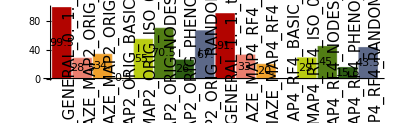

-Graphics-

-Graphics-

```mathematica
plotBooleanAsBarChart[selectData[sortedData,{"ID"->{"MAZE"}}],"SUCCESS",8]
```

```mathematica
printBooleanValueAsTable[sortedData,"SUCCESS",Operation->Total]
```

ID | PARAM FILE | SUCCESS
GP_1D_F_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_001.txt | 36.
GP_1D_F_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_002.txt | 28.
GP_1D_F_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_003.txt | 34.
GP_1D_F_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_004.txt | 28.
GP_1D_F_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_005.txt | 38.
GP_1D_F_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_006.txt | 26.
GP_1D_F_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_007.txt | 35.
GP_1D_F_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_008.txt | 31.
GP_1D_F_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_009.txt | 24.
GP_1D_F_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_010.txt | 25.
GP_1D_F_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_011.txt | 10.
GP_1D_F_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_012.txt | 13.
GP_1D_F_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_013.txt | 18.
GP_1D_F_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_014.txt | 17.
GP_1D_F_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_015.txt | 21.
GP_1D_F_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_016.txt | 16.
GP_1D_F_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_017.txt | 13.
GP_1D_F_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_018.txt | 9.
GP_1D_F_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_019.txt | 11.
GP_1D_F_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_020.txt | 9.
GP_1D_F_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_021.txt | 14.
GP_1D_F_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_022.txt | 11.
GP_1D_F_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_023.txt | 8.
GP_1D_F_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_024.txt | 10.
GP_1D_H_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_025.txt | 168.
GP_1D_H_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_026.txt | 176.
GP_1D_H_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_027.txt | 154.
GP_1D_H_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_028.txt | 154.
GP_1D_H_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_029.txt | 171.
GP_1D_H_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_030.txt | 175.
GP_1D_H_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_031.txt | 142.
GP_1D_H_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_032.txt | 155.
GP_1D_H_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_033.txt | 171.
GP_1D_H_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_034.txt | 166.
GP_1D_H_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_035.txt | 159.
GP_1D_H_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_036.txt | 89.
GP_1D_H_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_037.txt | 164.
GP_1D_H_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_038.txt | 167.
GP_1D_H_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_039.txt | 166.
GP_1D_H_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_040.txt | 84.
GP_1D_H_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_041.txt | 149.
GP_1D_H_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_042.txt | 43.
GP_1D_H_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_043.txt | 147.
GP_1D_H_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_044.txt | 53.
GP_1D_H_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_045.txt | 150.
GP_1D_H_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_046.txt | 36.
GP_1D_H_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_047.txt | 154.
GP_1D_H_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_048.txt | 46.
GP_2D_I_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_049.txt | 70.
GP_2D_I_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_050.txt | 78.
GP_2D_I_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_051.txt | 61.
GP_2D_I_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_052.txt | 61.
GP_2D_I_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_053.txt | 68.
GP_2D_I_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_054.txt | 59.
GP_2D_I_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_055.txt | 67.
GP_2D_I_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_056.txt | 67.
GP_2D_I_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_057.txt | 58.
GP_2D_I_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_058.txt | 52.
GP_2D_I_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_059.txt | 45.
GP_2D_I_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_060.txt | 54.
GP_2D_I_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_061.txt | 52.
GP_2D_I_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_062.txt | 56.
GP_2D_I_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_063.txt | 57.
GP_2D_I_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_064.txt | 37.
GP_2D_I_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_065.txt | 44.
GP_2D_I_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_066.txt | 30.
GP_2D_I_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_067.txt | 51.
GP_2D_I_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_068.txt | 39.
GP_2D_I_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_069.txt | 35.
GP_2D_I_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_070.txt | 28.
GP_2D_I_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_071.txt | 54.
GP_2D_I_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_072.txt | 32.
GP_2D_J_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_073.txt | 140.
GP_2D_J_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_074.txt | 154.
GP_2D_J_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_075.txt | 138.
GP_2D_J_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_076.txt | 130.
GP_2D_J_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_077.txt | 142.
GP_2D_J_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_078.txt | 146.
GP_2D_J_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_079.txt | 134.
GP_2D_J_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_080.txt | 125.
GP_2D_J_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_081.txt | 136.
GP_2D_J_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_082.txt | 117.
GP_2D_J_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_083.txt | 125.
GP_2D_J_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_084.txt | 113.
GP_2D_J_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_085.txt | 124.
GP_2D_J_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_086.txt | 123.
GP_2D_J_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_087.txt | 113.
GP_2D_J_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_088.txt | 110.
GP_2D_J_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_089.txt | 109.
GP_2D_J_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_090.txt | 89.
GP_2D_J_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_091.txt | 106.
GP_2D_J_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_092.txt | 100.
GP_2D_J_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_093.txt | 114.
GP_2D_J_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_094.txt | 95.
GP_2D_J_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_095.txt | 105.
GP_2D_J_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_096.txt | 98.
GP_2D_K_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_097.txt | 134.
GP_2D_K_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_098.txt | 151.
GP_2D_K_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_099.txt | 120.
GP_2D_K_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_100.txt | 129.
GP_2D_K_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_101.txt | 134.
GP_2D_K_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_102.txt | 154.
GP_2D_K_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_103.txt | 129.
GP_2D_K_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_104.txt | 130.
GP_2D_K_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_105.txt | 122.
GP_2D_K_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_106.txt | 119.
GP_2D_K_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_107.txt | 113.
GP_2D_K_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_108.txt | 91.
GP_2D_K_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_109.txt | 128.
GP_2D_K_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_110.txt | 123.
GP_2D_K_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_111.txt | 115.
GP_2D_K_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_112.txt | 101.
GP_2D_K_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_113.txt | 106.
GP_2D_K_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_114.txt | 88.
GP_2D_K_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_115.txt | 112.
GP_2D_K_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_116.txt | 88.
GP_2D_K_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_117.txt | 107.
GP_2D_K_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_118.txt | 86.
GP_2D_K_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_119.txt | 111.
GP_2D_K_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_120.txt | 89.
GP_3D_E_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_121.txt | 102.
GP_3D_E_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_122.txt | 101.
GP_3D_E_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_123.txt | 68.
GP_3D_E_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_124.txt | 61.
GP_3D_E_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_125.txt | 94.
GP_3D_E_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_126.txt | 100.
GP_3D_E_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_127.txt | 62.
GP_3D_E_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_128.txt | 67.
GP_3D_E_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_129.txt | 111.
GP_3D_E_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_130.txt | 115.
GP_3D_E_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_131.txt | 98.
GP_3D_E_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_132.txt | 93.
GP_3D_E_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_133.txt | 103.
GP_3D_E_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_134.txt | 96.
GP_3D_E_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_135.txt | 90.
GP_3D_E_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_136.txt | 105.
GP_3D_E_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_137.txt | 87.
GP_3D_E_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_138.txt | 62.
GP_3D_E_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_139.txt | 91.
GP_3D_E_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_140.txt | 62.
GP_3D_E_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_141.txt | 106.
GP_3D_E_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_142.txt | 69.
GP_3D_E_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_143.txt | 96.
GP_3D_E_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_144.txt | 55.
GP_3D_H_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_145.txt | 30.
GP_3D_H_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_146.txt | 36.
GP_3D_H_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_147.txt | 22.
GP_3D_H_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_148.txt | 24.
GP_3D_H_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_149.txt | 34.
GP_3D_H_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_150.txt | 32.
GP_3D_H_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_151.txt | 23.
GP_3D_H_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_152.txt | 23.
GP_3D_H_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_153.txt | 24.
GP_3D_H_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_154.txt | 26.
GP_3D_H_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_155.txt | 30.
GP_3D_H_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_156.txt | 6.
GP_3D_H_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_157.txt | 20.
GP_3D_H_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_158.txt | 29.
GP_3D_H_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_159.txt | 22.
GP_3D_H_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_160.txt | 4.
GP_3D_H_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_161.txt | 29.
GP_3D_H_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_162.txt | 1.
GP_3D_H_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_163.txt | 22.
GP_3D_H_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_164.txt | 4.
GP_3D_H_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_165.txt | 25.
GP_3D_H_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_166.txt | 1.
GP_3D_H_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_167.txt | 30.
GP_3D_H_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_168.txt | 2.
GP_3D_K_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_169.txt | 76.
GP_3D_K_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_170.txt | 83.
GP_3D_K_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_171.txt | 54.
GP_3D_K_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_172.txt | 52.
GP_3D_K_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_173.txt | 91.
GP_3D_K_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_174.txt | 84.
GP_3D_K_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_175.txt | 48.
GP_3D_K_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_176.txt | 48.
GP_3D_K_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_177.txt | 83.
GP_3D_K_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_178.txt | 62.
GP_3D_K_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_179.txt | 71.
GP_3D_K_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_180.txt | 23.
GP_3D_K_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_181.txt | 79.
GP_3D_K_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_182.txt | 81.
GP_3D_K_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_183.txt | 69.
GP_3D_K_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_184.txt | 20.
GP_3D_K_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_185.txt | 67.
GP_3D_K_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_186.txt | 29.
GP_3D_K_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_187.txt | 69.
GP_3D_K_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_188.txt | 26.
GP_3D_K_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_189.txt | 79.
GP_3D_K_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_190.txt | 29.
GP_3D_K_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_191.txt | 70.
GP_3D_K_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_192.txt | 24.
GP_4D_C_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_193.txt | 200.
GP_4D_C_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_194.txt | 200.
GP_4D_C_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_195.txt | 194.
GP_4D_C_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_196.txt | 192.
GP_4D_C_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_197.txt | 200.
GP_4D_C_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_198.txt | 200.
GP_4D_C_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_199.txt | 193.
GP_4D_C_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_200.txt | 191.
GP_4D_C_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_201.txt | 200.
GP_4D_C_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_202.txt | 180.
GP_4D_C_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_203.txt | 200.
GP_4D_C_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_204.txt | 130.
GP_4D_C_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_205.txt | 200.
GP_4D_C_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_206.txt | 200.
GP_4D_C_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_207.txt | 200.
GP_4D_C_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_208.txt | 130.
GP_4D_C_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_209.txt | 200.
GP_4D_C_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_210.txt | 122.
GP_4D_C_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_211.txt | 200.
GP_4D_C_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_212.txt | 123.
GP_4D_C_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_213.txt | 200.
GP_4D_C_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_214.txt | 111.
GP_4D_C_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_215.txt | 200.
GP_4D_C_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_216.txt | 106.
GP_4D_F_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_217.txt | 170.
GP_4D_F_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_218.txt | 174.
GP_4D_F_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_219.txt | 162.
GP_4D_F_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_220.txt | 150.
GP_4D_F_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_221.txt | 180.
GP_4D_F_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_222.txt | 175.
GP_4D_F_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_223.txt | 137.
GP_4D_F_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_224.txt | 159.
GP_4D_F_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_225.txt | 104.
GP_4D_F_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_226.txt | 88.
GP_4D_F_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_227.txt | 64.
GP_4D_F_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_228.txt | 61.
GP_4D_F_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_229.txt | 147.
GP_4D_F_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_230.txt | 146.
GP_4D_F_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_231.txt | 87.
GP_4D_F_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_232.txt | 49.
GP_4D_F_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_233.txt | 28.
GP_4D_F_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_234.txt | 0.
GP_4D_F_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_235.txt | 27.
GP_4D_F_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_236.txt | 0.
GP_4D_F_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_237.txt | 31.
GP_4D_F_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_238.txt | 0.
GP_4D_F_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_239.txt | 32.
GP_4D_F_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_240.txt | 0.
GP_4D_G_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_241.txt | 164.
GP_4D_G_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_242.txt | 165.
GP_4D_G_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_243.txt | 157.
GP_4D_G_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_244.txt | 142.
GP_4D_G_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_245.txt | 179.
GP_4D_G_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_246.txt | 175.
GP_4D_G_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_247.txt | 143.
GP_4D_G_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_248.txt | 154.
GP_4D_G_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_249.txt | 73.
GP_4D_G_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_250.txt | 71.
GP_4D_G_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_251.txt | 54.
GP_4D_G_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_252.txt | 54.
GP_4D_G_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_253.txt | 126.
GP_4D_G_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_254.txt | 127.
GP_4D_G_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_255.txt | 54.
GP_4D_G_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_256.txt | 61.
GP_4D_G_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_257.txt | 15.
GP_4D_G_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_258.txt | 0.
GP_4D_G_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_259.txt | 18.
GP_4D_G_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_260.txt | 0.
GP_4D_G_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_261.txt | 22.
GP_4D_G_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_262.txt | 0.
GP_4D_G_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_263.txt | 23.
GP_4D_G_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_264.txt | 0.
GP_4D_FC55_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_265.txt | 193.
GP_4D_FC55_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_266.txt | 193.
GP_4D_FC55_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_267.txt | 183.
GP_4D_FC55_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_268.txt | 184.
GP_4D_FC55_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_269.txt | 199.
GP_4D_FC55_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_270.txt | 200.
GP_4D_FC55_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_271.txt | 176.
GP_4D_FC55_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_272.txt | 175.
GP_4D_FC55_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_273.txt | 200.
GP_4D_FC55_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_274.txt | 122.
GP_4D_FC55_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_275.txt | 186.
GP_4D_FC55_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_276.txt | 5.
GP_4D_FC55_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_277.txt | 198.
GP_4D_FC55_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_278.txt | 195.
GP_4D_FC55_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_279.txt | 181.
GP_4D_FC55_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_280.txt | 2.
GP_4D_FC55_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_281.txt | 110.
GP_4D_FC55_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_282.txt | 4.
GP_4D_FC55_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_283.txt | 106.
GP_4D_FC55_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_284.txt | 1.
GP_4D_FC55_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_285.txt | 108.
GP_4D_FC55_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_286.txt | 4.
GP_4D_FC55_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_287.txt | 128.
GP_4D_FC55_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_288.txt | 0.
GP_MAZE_MAP2_ORIG_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_289.txt | 190.
GP_MAZE_MAP2_ORIG_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_291.txt | 188.
GP_MAZE_MAP2_ORIG_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_293.txt | 181.
GP_MAZE_MAP2_ORIG_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_295.txt | 181.
GP_MAZE_MAP2_ORIG_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_297.txt | 199.
GP_MAZE_MAP2_ORIG_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_299.txt | 195.
GP_MAZE_MAP2_ORIG_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_301.txt | 179.
GP_MAZE_MAP2_ORIG_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_303.txt | 185.
GP_MAZE_MAP2_ORIG_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_305.txt | 125.
GP_MAZE_MAP2_ORIG_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_307.txt | 22.
GP_MAZE_MAP2_ORIG_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_309.txt | 117.
GP_MAZE_MAP2_ORIG_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_311.txt | 4.
GP_MAZE_MAP2_ORIG_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_313.txt | 181.
GP_MAZE_MAP2_ORIG_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_315.txt | 182.
GP_MAZE_MAP2_ORIG_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_317.txt | 125.
GP_MAZE_MAP2_ORIG_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_319.txt | 4.
GP_MAZE_MAP2_ORIG_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_321.txt | 66.
GP_MAZE_MAP2_ORIG_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_323.txt | 2.
GP_MAZE_MAP2_ORIG_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_325.txt | 73.
GP_MAZE_MAP2_ORIG_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_327.txt | 2.
GP_MAZE_MAP2_ORIG_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_329.txt | 86.
GP_MAZE_MAP2_ORIG_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_331.txt | 1.
GP_MAZE_MAP2_ORIG_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_333.txt | 82.
GP_MAZE_MAP2_ORIG_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_335.txt | 0.
GP_MAZE_MAP4_RF4_GENERAL_0._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_290.txt | 164.
GP_MAZE_MAP4_RF4_GENERAL_1._1._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_292.txt | 154.
GP_MAZE_MAP4_RF4_GENERAL_0._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_294.txt | 147.
GP_MAZE_MAP4_RF4_GENERAL_1._1._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_296.txt | 156.
GP_MAZE_MAP4_RF4_GENERAL_0._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_298.txt | 172.
GP_MAZE_MAP4_RF4_GENERAL_1._1._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_300.txt | 182.
GP_MAZE_MAP4_RF4_GENERAL_0._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_302.txt | 162.
GP_MAZE_MAP4_RF4_GENERAL_1._1._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_304.txt | 150.
GP_MAZE_MAP4_RF4_GENERAL_0._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_306.txt | 44.
GP_MAZE_MAP4_RF4_GENERAL_1._2._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_308.txt | 16.
GP_MAZE_MAP4_RF4_GENERAL_0._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_310.txt | 37.
GP_MAZE_MAP4_RF4_GENERAL_1._2._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_312.txt | 0.
GP_MAZE_MAP4_RF4_GENERAL_0._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_314.txt | 110.
GP_MAZE_MAP4_RF4_GENERAL_1._2._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_316.txt | 118.
GP_MAZE_MAP4_RF4_GENERAL_0._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_318.txt | 33.
GP_MAZE_MAP4_RF4_GENERAL_1._2._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_320.txt | 0.
GP_MAZE_MAP4_RF4_GENERAL_0._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_322.txt | 33.
GP_MAZE_MAP4_RF4_GENERAL_1._10._false_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_324.txt | 0.
GP_MAZE_MAP4_RF4_GENERAL_0._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_326.txt | 25.
GP_MAZE_MAP4_RF4_GENERAL_1._10._false_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_328.txt | 0.
GP_MAZE_MAP4_RF4_GENERAL_0._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_330.txt | 33.
GP_MAZE_MAP4_RF4_GENERAL_1._10._true_false_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_332.txt | 0.
GP_MAZE_MAP4_RF4_GENERAL_0._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_334.txt | 16.
GP_MAZE_MAP4_RF4_GENERAL_1._10._true_true_0.4_5. | GP_GPEFS_GENERAL_GECCO/parameters_336.txt | 0.

```mathematica
printBooleanRanksAsTable[sortedData,"SUCCESS",24]//N
```

ID | GP.DISTANCE_GENERAL_C | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | PARALLEL.FORCE_THREADS | RANK
8. | 1. | true | 1. | true | 2. | 19.
7. | 0. | true | 1. | true | 3. | 18.
6. | 1. | true | 1. | false | 2. | 23.5
5. | 0. | true | 1. | false | 3. | 23.5
4. | 1. | false | 1. | true | 2. | 18.5
3. | 0. | false | 1. | true | 3. | 17.
2. | 1. | false | 1. | false | 2. | 20.
1. | 0. | false | 1. | false | 3. | 22.
16. | 1. | true | 2. | true | 2. | 4.5
15. | 0. | true | 2. | true | 3. | 12.25
14. | 1. | true | 2. | false | 2. | 17.5
13. | 0. | true | 2. | false | 3. | 16.
12. | 1. | false | 2. | true | 2. | 4.5
11. | 0. | false | 2. | true | 3. | 12.5
10. | 1. | false | 2. | false | 2. | 7.25
9. | 0. | false | 2. | false | 3. | 13.75
24. | 1. | true | 10. | true | 2. | 2.25
23. | 0. | true | 10. | true | 3. | 8.75
22. | 1. | true | 10. | false | 2. | 2.75
21. | 0. | true | 10. | false | 3. | 11.
20. | 1. | false | 10. | true | 2. | 3.5
19. | 0. | false | 10. | true | 3. | 9.
18. | 1. | false | 10. | false | 2. | 3.5
17. | 0. | false | 10. | false | 3. | 9.5

## Experiments IV

```mathematica
(*names={"HGP_RANDOMPAR","HGP_BASICPAR","HGP_RESTO2PAR","HGP_TREEPPAR","HGP_TREEP2PAR"};*)
(*names={"HNEAT_BASIC","HNEAT_NOMULT","HNEAT_ALL","HGP","HGP_RANDOM","HGP_BASIC","HGP_RESTO2","HGP_TREEP","HGP_TREEP2"};*)
(*names={"HNEAT_NOMULT","HGP","HGP_GPEFS_NOGENERAL_GECCO"};*)
names={"HNEAT_GECCO","HGP","HGP_GPEFS_NOGENERAL_GECCO","HGP_GPEFS_GENERAL_BEST_GECCO","ROBO_GECCO"};
(*names={"HGP_TREEP2PAR"};*)
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","RECO.GENERATOR","GPAT.DISTANCE","GP.DISTANCE","GP.DISTANCE_GENERAL_C","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPEFS.SPECIES_SIZE_MEAN","NEAT.distanceDelta"},{"ZFC55"->"FC55","hyper.experiments.reco.problem.PatternGeneratorXOR"->"",RegularExpression["hyper.experiments.reco.problem.PatternGenerator"]->""}];
changingParameters[data]
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.DISTANCE,GP.DISTANCE_GENERAL_C,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_GENERATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.MUTATION_SUBTREE_PROBABLITY,GP.TYPE,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PRINT.finished,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.generation,PRINT.progress,PRINT.progressShowHyperNet,PRINT.progressShowProblem,PRINT.storeRun,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,SOLVER}

```mathematica
saveData[sortedData,"HGP_GPEFS_GENERAL_GECCO2"]
```

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE_WEIGHTED_C1"->{0.5,2.}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
sdata=selectData[data,{"PROBLEM"->"XOR"}];
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GP.DISTANCE_GENERAL_C"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","RECO.GENERATOR","MAZE.MAP","GPAT.DISTANCE","GP.TARGET_FITNESS","GP.DISTANCE","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN","PROBLEM","GPAT.DISTANCE_WEIGHTED_C1"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | RECO.GENERATOR | MAZE.MAP | GPAT.DISTANCE | GP.TARGET_FITNESS | GP.DISTANCE | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | PROBLEM | GPAT.DISTANCE_WEIGHTED_C1
GP_FC_GENERAL_0._2._false_false | HGP_GPEFS_GENERAL_BEST_GECCO/parameters_001.txt | GP |  | FC |  |  |  |  | GENERAL | 0.4 |  | FIND_CLUSTER | 
NEAT_FC_3. | HNEAT_GECCO/parameters_001.txt | NEAT |  | FC |  |  |  |  |  |  |  | FIND_CLUSTER | 
GP_FC | HGP/parameters_001.txt | GP |  | FC |  |  |  |  |  |  |  | FIND_CLUSTER | 
GP_FC_BASIC | HGP_GPEFS_NOGENERAL_GECCO/parameters_001.txt | GP |  | FC |  |  |  |  | BASIC | 0.4 |  | FIND_CLUSTER | 
GP_FC_ISO | HGP_GPEFS_NOGENERAL_GECCO/parameters_006.txt | GP |  | FC |  |  |  |  | ISO | 0.4 |  | FIND_CLUSTER | 
GP_FC_NODES | HGP_GPEFS_NOGENERAL_GECCO/parameters_011.txt | GP |  | FC |  |  |  |  | NODES | 0.4 |  | FIND_CLUSTER | 
GP_FC_PHENO | HGP_GPEFS_NOGENERAL_GECCO/parameters_016.txt | GP |  | FC |  |  |  |  | PHENO | 0.4 |  | FIND_CLUSTER | 
GP_FC_RANDOM | HGP_GPEFS_NOGENERAL_GECCO/parameters_021.txt | GP |  | FC |  |  |  |  | RANDOM | 0.4 |  | FIND_CLUSTER | 
GP_RECO1D_CopyMirrored1D_GENERAL_0._2._false_false | HGP_GPEFS_GENERAL_BEST_GECCO/parameters_002.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  |  | GENERAL | 0.4 |  | RECO | 
NEAT_RECO1D_CopyMirrored1D_3. | HNEAT_GECCO/parameters_002.txt | NEAT |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  |  |  |  |  | RECO | 
GP_RECO1D_CopyMirrored1D | HGP/parameters_002.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  |  |  |  |  | RECO | 
GP_RECO1D_CopyMirrored1D_BASIC | HGP_GPEFS_NOGENERAL_GECCO/parameters_002.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  |  | BASIC | 0.4 |  | RECO | 
GP_RECO1D_CopyMirrored1D_ISO | HGP_GPEFS_NOGENERAL_GECCO/parameters_007.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  |  | ISO | 0.4 |  | RECO | 
GP_RECO1D_CopyMirrored1D_NODES | HGP_GPEFS_NOGENERAL_GECCO/parameters_012.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  |  | NODES | 0.4 |  | RECO | 
GP_RECO1D_CopyMirrored1D_PHENO | HGP_GPEFS_NOGENERAL_GECCO/parameters_017.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  |  | PHENO | 0.4 |  | RECO | 
GP_RECO1D_CopyMirrored1D_RANDOM | HGP_GPEFS_NOGENERAL_GECCO/parameters_022.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  |  | RANDOM | 0.4 |  | RECO | 
GP_RECO1D_CopyRotated1D_GENERAL_0._1._false_true | HGP_GPEFS_GENERAL_BEST_GECCO/parameters_003.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  |  | GENERAL | 0.4 |  | RECO | 
NEAT_RECO1D_CopyRotated1D_3. | HNEAT_GECCO/parameters_004.txt | NEAT |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  |  |  |  |  | RECO | 
GP_RECO1D_CopyRotated1D | HGP/parameters_004.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  |  |  |  |  | RECO | 
GP_RECO1D_CopyRotated1D_BASIC | HGP_GPEFS_NOGENERAL_GECCO/parameters_004.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  |  | BASIC | 0.4 |  | RECO | 
GP_RECO1D_CopyRotated1D_ISO | HGP_GPEFS_NOGENERAL_GECCO/parameters_009.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  |  | ISO | 0.4 |  | RECO | 
GP_RECO1D_CopyRotated1D_NODES | HGP_GPEFS_NOGENERAL_GECCO/parameters_014.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  |  | NODES | 0.4 |  | RECO | 
GP_RECO1D_CopyRotated1D_PHENO | HGP_GPEFS_NOGENERAL_GECCO/parameters_019.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  |  | PHENO | 0.4 |  | RECO | 
GP_RECO1D_CopyRotated1D_RANDOM | HGP_GPEFS_NOGENERAL_GECCO/parameters_024.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  |  | RANDOM | 0.4 |  | RECO | 
GP_RECO1D_CopyShifted1D_GENERAL_0._10._false_false | HGP_GPEFS_GENERAL_BEST_GECCO/parameters_004.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  |  | GENERAL | 0.4 |  | RECO | 
NEAT_RECO1D_CopyShifted1D_3. | HNEAT_GECCO/parameters_003.txt | NEAT |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  |  |  |  |  | RECO | 
GP_RECO1D_CopyShifted1D | HGP/parameters_003.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  |  |  |  |  | RECO | 
GP_RECO1D_CopyShifted1D_BASIC | HGP_GPEFS_NOGENERAL_GECCO/parameters_003.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  |  | BASIC | 0.4 |  | RECO | 
GP_RECO1D_CopyShifted1D_ISO | HGP_GPEFS_NOGENERAL_GECCO/parameters_008.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  |  | ISO | 0.4 |  | RECO | 
GP_RECO1D_CopyShifted1D_NODES | HGP_GPEFS_NOGENERAL_GECCO/parameters_013.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  |  | NODES | 0.4 |  | RECO | 
GP_RECO1D_CopyShifted1D_PHENO | HGP_GPEFS_NOGENERAL_GECCO/parameters_018.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  |  | PHENO | 0.4 |  | RECO | 
GP_RECO1D_CopyShifted1D_RANDOM | HGP_GPEFS_NOGENERAL_GECCO/parameters_023.txt | GP |  | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  |  | RANDOM | 0.4 |  | RECO | 
GP_ROBO_GENERAL_0._1._true_false | ROBO_GECCO/parameters_002.txt | GP |  | ROBO |  |  |  | 0.798 | GENERAL | 0.4 |  | ROBOTS | 
GP_ROBO_BASIC | ROBO_GECCO/parameters_001.txt | GP |  | ROBO |  |  |  | 0.798 | BASIC | 0.4 |  | ROBOTS | 
GP_ROBO_PHENO | ROBO_GECCO/parameters_003.txt | GP |  | ROBO |  |  |  | 0.798 | PHENO | 0.4 |  | ROBOTS | 
GP_ROBO_ISO | ROBO_GECCO/parameters_004.txt | GP |  | ROBO |  |  |  | 0.798 | ISO | 0.4 |  | ROBOTS | 
GP_ROBO_NODES | ROBO_GECCO/parameters_005.txt | GP |  | ROBO |  |  |  | 0.798 | NODES | 0.4 |  | ROBOTS | 
GP_ROBO_PHENO | ROBO_GECCO/parameters_006.txt | GP |  | ROBO |  |  |  | 0.798 | PHENO | 0.4 |  | ROBOTS | 
GP_ROBO_RANDOM | ROBO_GECCO/parameters_007.txt | GP |  | ROBO |  |  |  | 0.798 | RANDOM | 0.4 |  | ROBOTS | 
NEAT_ROBO_3. | ROBO_GECCO/parameters_008.txt | NEAT |  | ROBO |  |  |  | 0.798 |  |  |  | ROBOTS | 
GP_XOR_GENERAL_1._1._true_false | HGP_GPEFS_GENERAL_BEST_GECCO/parameters_005.txt | GP |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  |  | GENERAL | 0.4 |  | XOR | 
NEAT_XOR_3. | HNEAT_GECCO/parameters_005.txt | NEAT |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  |  |  |  |  | XOR | 
GP_XOR | HGP/parameters_005.txt | GP |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  |  |  |  |  | XOR | 
GP_XOR_BASIC | HGP_GPEFS_NOGENERAL_GECCO/parameters_005.txt | GP |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  |  | BASIC | 0.4 |  | XOR | 
GP_XOR_ISO | HGP_GPEFS_NOGENERAL_GECCO/parameters_010.txt | GP |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  |  | ISO | 0.4 |  | XOR | 
GP_XOR_NODES | HGP_GPEFS_NOGENERAL_GECCO/parameters_015.txt | GP |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  |  | NODES | 0.4 |  | XOR | 
GP_XOR_PHENO | HGP_GPEFS_NOGENERAL_GECCO/parameters_020.txt | GP |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  |  | PHENO | 0.4 |  | XOR | 
GP_XOR_RANDOM | HGP_GPEFS_NOGENERAL_GECCO/parameters_025.txt | GP |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  |  | RANDOM | 0.4 |  | XOR |

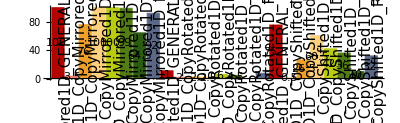

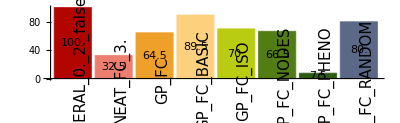

-Graphics-

-Graphics-

-Graphics-

-Graphics-

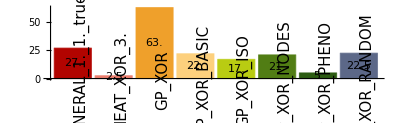

-Graphics-

-Graphics-

```mathematica
plotBooleanAsBarChart[selectData[sortedData,{"ID"->"RECO1D"}],"SUCCESS",8]
```

```mathematica
printBooleanValueAsTable[sortedData,"SUCCESS",Operation->Total];
```

```mathematica
fcomp={360,242};
testFisherExact[{{fcomp[[1]],1600-fcomp[[1]]},{fcomp[[2]],1600-fcomp[[2]]}}]
```

1.12259×10^-7

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSFG",10]
```

```mathematica
printBooleanRanksAsTable[sortedData,"SUCCESS",21]//N
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
21. | 1. | 20. | 3.72
19. | 1. | 5. | 4.52
20. | 1. | 10. | 4.82
18. | 0.8 | 20. | 6.82
9. | 0.2 | 20. | 8.46
17. | 0.8 | 10. | 8.6
16. | 0.8 | 5. | 8.88
15. | 0.6 | 20. | 9.78
6. | 0.1 | 20. | 10.26
12. | 0.4 | 20. | 11.18
14. | 0.6 | 10. | 11.66
13. | 0.6 | 5. | 12.14
3. | 0.05 | 20. | 12.46
8. | 0.2 | 10. | 13.68
1. | 0.05 | 5. | 14.02
4. | 0.1 | 5. | 14.32
11. | 0.4 | 10. | 14.48
5. | 0.1 | 10. | 14.52
2. | 0.05 | 10. | 14.9
7. | 0.2 | 5. | 15.62
10. | 0.4 | 5. | 16.16

```mathematica
RANDOM
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
4. | 0.1 | 5. | 6.7
1. | 0.05 | 5. | 7.2
21. | 1. | 20. | 7.6
19. | 1. | 5. | 8.6
20. | 1. | 10. | 9.2
8. | 0.2 | 10. | 9.4
5. | 0.1 | 10. | 9.5
7. | 0.2 | 5. | 9.7
9. | 0.2 | 20. | 10.5
6. | 0.1 | 20. | 10.5
2. | 0.05 | 10. | 10.5
17. | 0.8 | 10. | 11.7
14. | 0.6 | 10. | 11.8
16. | 0.8 | 5. | 12.
18. | 0.8 | 20. | 12.3
3. | 0.05 | 20. | 12.7
12. | 0.4 | 20. | 13.4
13. | 0.6 | 5. | 14.
10. | 0.4 | 5. | 14.1
15. | 0.6 | 20. | 14.4
11. | 0.4 | 10. | 15.2

```mathematica
BASIC
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
19. | 1. | 5. | 3.
21. | 1. | 20. | 3.6
20. | 1. | 10. | 4.4
9. | 0.2 | 20. | 6.3
17. | 0.8 | 10. | 7.
6. | 0.1 | 20. | 7.1
3. | 0.05 | 20. | 8.6
18. | 0.8 | 20. | 8.8
16. | 0.8 | 5. | 9.6
12. | 0.4 | 20. | 12.4
14. | 0.6 | 10. | 12.7
4. | 0.1 | 5. | 13.1
8. | 0.2 | 10. | 13.3
15. | 0.6 | 20. | 13.6
5. | 0.1 | 10. | 13.8
1. | 0.05 | 5. | 13.9
13. | 0.6 | 5. | 14.
2. | 0.05 | 10. | 14.3
7. | 0.2 | 5. | 15.4
11. | 0.4 | 10. | 17.
10. | 0.4 | 5. | 19.1

```mathematica
RESTO2
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
21. | 1. | 20. | 2.7
20. | 1. | 10. | 2.7
18. | 0.8 | 20. | 4.1
19. | 1. | 5. | 4.6
15. | 0.6 | 20. | 6.6
9. | 0.2 | 20. | 6.6
13. | 0.6 | 5. | 8.8
17. | 0.8 | 10. | 9.
16. | 0.8 | 5. | 9.4
6. | 0.1 | 20. | 9.4
14. | 0.6 | 10. | 11.4
12. | 0.4 | 20. | 12.5
11. | 0.4 | 10. | 13.5
3. | 0.05 | 20. | 14.2
1. | 0.05 | 5. | 15.9
10. | 0.4 | 5. | 16.
8. | 0.2 | 10. | 16.
2. | 0.05 | 10. | 16.2
4. | 0.1 | 5. | 16.3
5. | 0.1 | 10. | 17.1
7. | 0.2 | 5. | 18.

```mathematica
TREEP
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
21. | 1. | 20. | 1.9
19. | 1. | 5. | 3.3
18. | 0.8 | 20. | 3.7
20. | 1. | 10. | 4.3
16. | 0.8 | 5. | 6.2
9. | 0.2 | 20. | 7.8
17. | 0.8 | 10. | 7.9
15. | 0.6 | 20. | 8.9
6. | 0.1 | 20. | 10.2
12. | 0.4 | 20. | 11.5
14. | 0.6 | 10. | 11.7
13. | 0.6 | 5. | 12.4
3. | 0.05 | 20. | 13.1
11. | 0.4 | 10. | 13.4
8. | 0.2 | 10. | 14.7
10. | 0.4 | 5. | 15.7
4. | 0.1 | 5. | 16.
1. | 0.05 | 5. | 16.3
5. | 0.1 | 10. | 16.5
2. | 0.05 | 10. | 17.
7. | 0.2 | 5. | 18.5

```mathematica
TREEP2
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
21. | 1. | 20. | 2.8
19. | 1. | 5. | 3.1
20. | 1. | 10. | 3.5
18. | 0.8 | 20. | 5.2
15. | 0.6 | 20. | 5.4
12. | 0.4 | 20. | 6.1
16. | 0.8 | 5. | 7.2
17. | 0.8 | 10. | 7.4
14. | 0.6 | 10. | 10.7
9. | 0.2 | 20. | 11.1
13. | 0.6 | 5. | 11.5
11. | 0.4 | 10. | 13.3
3. | 0.05 | 20. | 13.7
6. | 0.1 | 20. | 14.1
8. | 0.2 | 10. | 15.
5. | 0.1 | 10. | 15.7
10. | 0.4 | 5. | 15.9
7. | 0.2 | 5. | 16.5
2. | 0.05 | 10. | 16.5
1. | 0.05 | 5. | 16.8
4. | 0.1 | 5. | 19.5

## Statistics

```mathematica
testMannWhitney[data,"GPAT_H","GPAT_H2","BSF"]
```

median 1: 0.952853

median 2: 0.949325

mean 1: 0.754262

mean 2: 0.528663

variance 1: 0.135817

variance 2: 0.222969

higher/lower variance ratio: 1.64169

U stat: 22636

P-value: 0.0226329

The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.

```mathematica
testKruskalWallis[data,{"GP_H","GPAT_H2"},"BSF"]
```

| GPAT_H | GPAT_H2
Mean | 0.754262 | 0.528663
Variance | 0.952853 | 0.949325
Variance | 0.135817 | 0.222969

LocationEquivalenceTest::ntsymmd: The p-value in 1.14305×10^-13, resulting from a test for symmetry, is below 0.05. The tests in {"KruskalWallis"} require that the data is symmetric about a common median.

| Statistic | P-Value
Kruskal-Wallis | 5.19838 | 0.0224202

```mathematica
testFisherExact[{{90,10},{82,18}}]
```

0.152819

```mathematica
testFisherExact[sortedData,"GPAT_E","GPATGP_E","SUCCESS",TwoSided->True,PValueOnly->False]
```

| GPAT_E | GPATGP_E
true | 0. | 1.
false | 200. | 199.
p-value | 1. |

```mathematica
testFisherExactAll[sortedData,"SUCCESS",0.05,TwoSided->True]
```

| 2 | 3 | 4 | 5 | 6
1 | 0.0900213 | 8.70428×10^-7 | 2.99731×10^-15 | 4.39804×10^-33 | 2.71714×10^-43
2 |  | 0.00174071 | 7.22079×10^-10 | 4.23269×10^-25 | 2.75651×10^-34
3 |  |  | 0.00295964 | 3.33437×10^-13 | 3.18256×10^-20
4 |  |  |  | 0.0000196958 | 4.04422×10^-10
5 |  |  |  |  | 0.0552636

## Expressions

```mathematica
sortConfigurationResults[sortedData,"A","BSF",10]
```

1 | 0.996687
12 | 0.983575
100 | 0.970368
78 | 0.96933
10 | 0.968461
60 | 0.968217
79 | 0.963918
73 | 0.958339
68 | 0.956159
35 | 0.955737

```mathematica
Expand[1.5*x1*x2+2.3*x1+x2*x3*x4-1.1*x3]
```

2.3 x1+1.5 x1 x2-1.1 x3+x2 x3 x4

```mathematica
(res=sortConfigurationResults[sortedData,"GP3D_H2","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {x_2 (-1.+x_1 (x_3+x_2 x_3))} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+x_1 x_3+x_1 x_2 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_2 (x_1+x_1 x_2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1 x_2^2 x_3+x_2 (-1.+x_1 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1-1. x_2+x_1 (-1.+x_2 x_3+x_2^2 x_3)} | {0.-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+(x_1+x_1 x_2) x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {1.08185×10^-8-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {1.08185×10^-8-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 (4.44373×10^-11+x_2 x_3+x_2^2 x_3)} | {4.44373×10^-11 x_1-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.

```mathematica
(res=sortConfigurationResults[sortedData,"12","BSF",25,Output->"Expressions"]/.{x0->x})
```

Gen | Expression | Expanded | f
last | {0.09977 x (x+Sin[0.787112 ⅇ^(-x^2)])} | {0.09977 x^2+0.09977 x Sin[0.787112 ⅇ^(-x^2)]} | 0.995529
last | {0.0646032 x (ⅇ^(-x^2)+1.55385 x)-0.0344501 Sin[1.-ⅇ^(-x^2)]} | {0.0646032 ⅇ^(-x^2) x+0.100383 x^2-0.0344501 Sin[1.-ⅇ^(-x^2)]} | 0.995316
last | {0.100061 x (0.0156719+x)} | {0.00156814 x+0.100061 x^2} | 0.995278
last | {ⅇ^(-11.8063-Sin[x]^2)+0.0999739 x (0.021377+x)} | {ⅇ^(-11.8063-Sin[x]^2)+0.00213714 x+0.0999739 x^2} | 0.995253
last | {0.100195 x^2} | {0.100195 x^2} | 0.995163
last | {0.0997882 x^2} | {0.0997882 x^2} | 0.995147
last | {-0.0015477+0.100253 x^2} | {-0.0015477+0.100253 x^2} | 0.995127
last | {0.0995871 x^2} | {0.0995871 x^2} | 0.994844
last | {0.0995752 x^2} | {0.0995752 x^2} | 0.99482
last | {0.100443 x^2} | {0.100443 x^2} | 0.994783
last | {0.0999352 (-0.0328145+x) x} | {-0.00327932 x+0.0999352 x^2} | 0.994597
last | {0.0994062 x^2} | {0.0994062 x^2} | 0.994405
last | {0.100651 x^2} | {0.100651 x^2} | 0.994233
last | {4.35401×10^-11+0.100887 x (ⅇ^(-x^2)+x)} | {4.35401×10^-11+0.100887 ⅇ^(-x^2) x+0.100887 x^2} | 0.993847
last | {0.10084 x^2} | {0.10084 x^2} | 0.993554
last | {0.0993273 x (ⅇ^(-33.9284 (3.47822+x)^2)+x)} | {0.0993273 ⅇ^(-33.9284 (3.47822+x)^2) x+0.0993273 x^2} | 0.993273
last | {0.0990122 x^2} | {0.0990122 x^2} | 0.992907
last | {-0.000371379+0.0990141 x^2} | {-0.000371379+0.0990141 x^2} | 0.992889
last | {Sin[0.129682 x] (x-Sin[0.336709 x]-0.196058 Sin[x])} | {x Sin[0.129682 x]-Sin[0.129682 x] Sin[0.336709 x]-0.196058 Sin[0.129682 x] Sin[x]} | 0.992606
last | {0.101464 (-0.763579+x (0.0208029+x))} | {-0.0774756+0.00211074 x+0.101464 x^2} | 0.992428
last | {0.0988539 x^2} | {0.0988539 x^2} | 0.992097
last | {0.101382 x (ⅇ^(-0.332217 x^2)+x)} | {0.101382 ⅇ^(-0.332217 x^2) x+0.101382 x^2} | 0.99195
last | {(0.815193 x^2 (-0.632121 ⅇ^(-(4.80488+x)^2)+x+ⅇ^(-x^2) (2.03518+x)) ArcTan[x])/(√(1+140.445 x^2))} | {(1.65907 ⅇ^(-x^2) x^2 ArcTan[x])/(√(1+140.445 x^2))-(0.5153 ⅇ^(-(4.80488+x)^2) x^2 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 x^3 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 ⅇ^(-x^2) x^3 ArcTan[x])/(√(1+140.445 x^2))} | 0.991336
last | {0.10128 x^2} | {0.10128 x^2} | 0.991321
last | {0.0989743 x (0.0785205+x)} | {0.00777151 x+0.0989743 x^2} | 0.991136

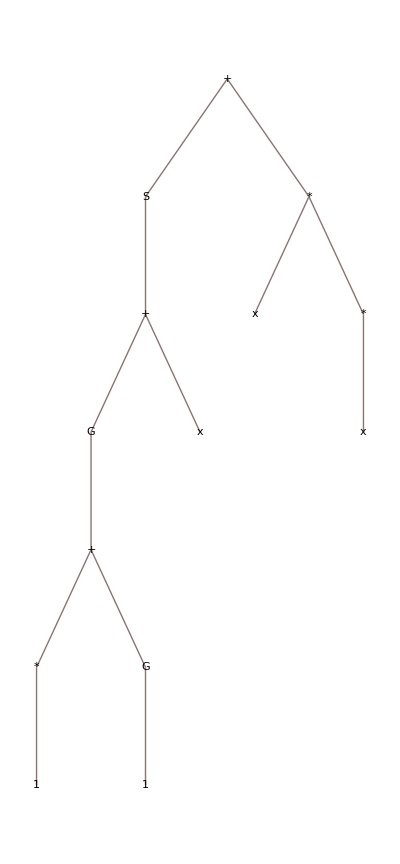
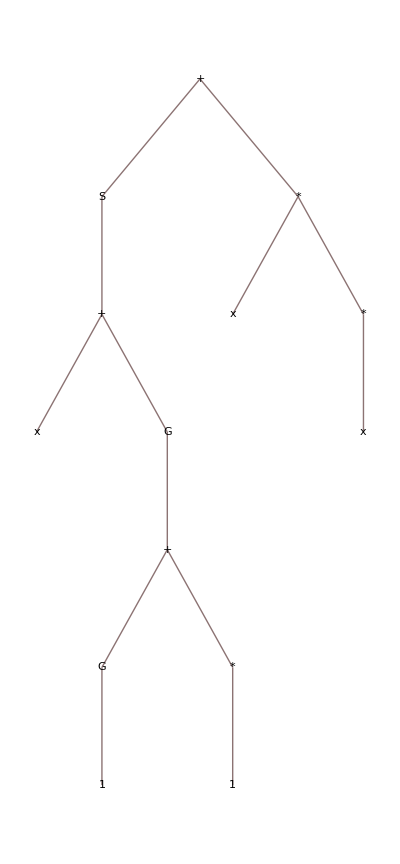
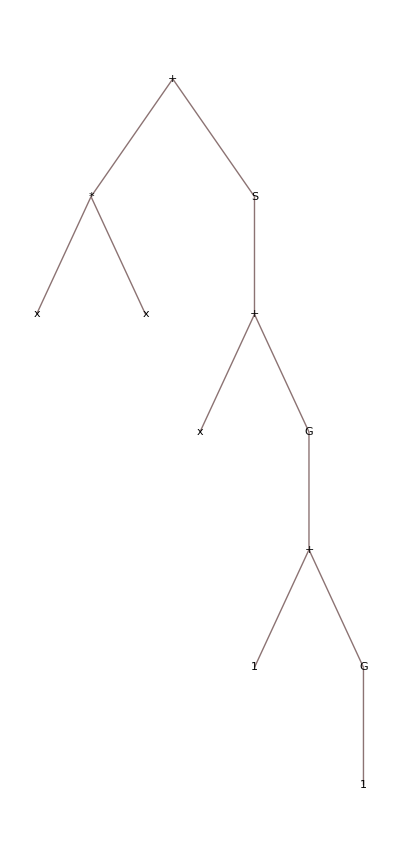
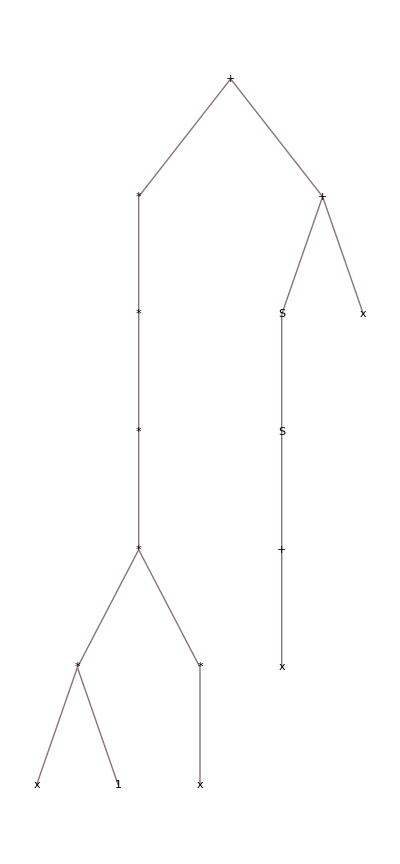
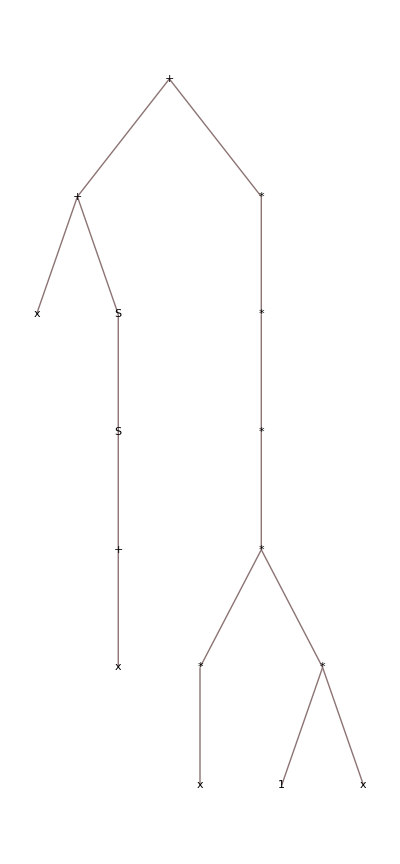
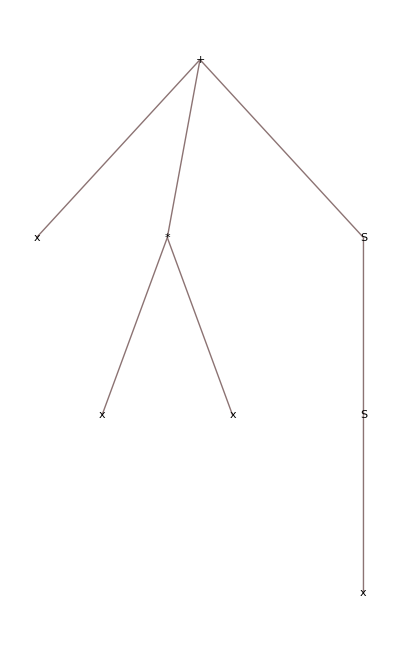
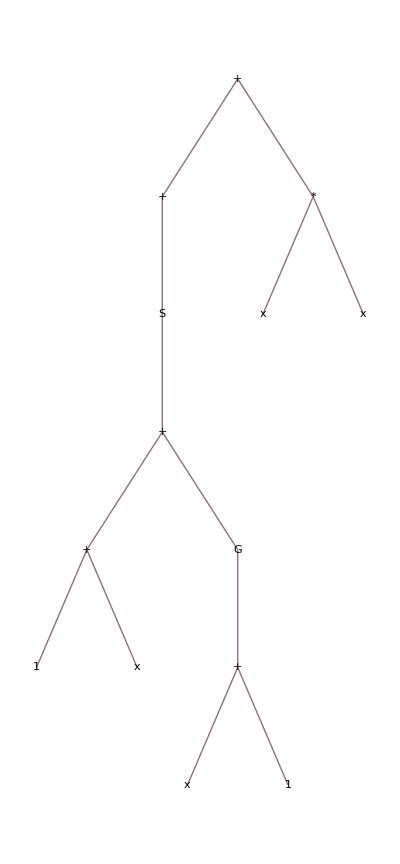
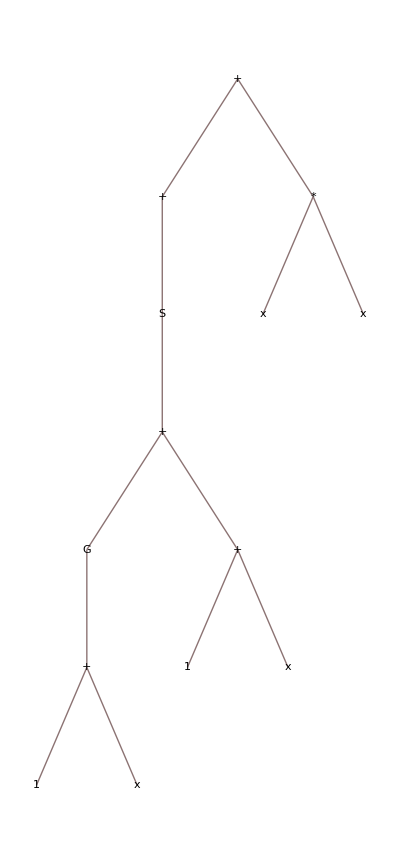
Gen | Genome | Sorted | Simplified | f
last | -Graphics- | -Graphics- | -Graphics- | 0.99656
last | -Graphics- | -Graphics- | -Graphics- | 0.983261
last | -Graphics- | -Graphics- | -Graphics- | 0.978954
last | -Graphics- | -Graphics- | -Graphics- | 0.978529
last | -Graphics- | -Graphics- | -Graphics- | 0.957386
last | -Graphics- | -Graphics- | -Graphics- | 0.956843
last | -Graphics- | -Graphics- | -Graphics- | 0.952837
last | -Graphics- | -Graphics- | -Graphics- | 0.951168
last | -Graphics- | -Graphics- | -Graphics- | 0.940757
last | -Graphics- | -Graphics- | -Graphics- | 0.852304

```mathematica
(res=sortConfigurationResults[sortedData,"A","BSF",10,Output->"BSFGenomes"]/.{x0->x})
```

```mathematica
Export["GP_H2.pdf",%]
```

GP_H2.pdf